```mathematica
hif=Import[FileNameJoin[{NotebookDirectory[],"features/english_hindi.csv"}]];
frf=Import[FileNameJoin[{NotebookDirectory[],"features/english_french.csv"}]];
```

```mathematica
enumerate[l_]:=MapIndexed[{#2[[1]],#1}&,l]
Juxt[f__]:=With[{x=#},Map[#[x]&,{f}]]&
MultiJuxt[f__]:=With[{l=#},MapIndexed[#1@l[[#2[[1]] ]]&,{f}]]&
AggregateCols[f__]:=MultiJuxt[f]@Transpose@#&
```

# Mutual Information/Feature Selection

```mathematica
rr=Dispatch[#[[1]]->#[[2]]&/@Transpose@ReplacePart[#,2->Map[(Total@#+1)/2&,#]&@Partition[{0}~Join~Accumulate@#[[2]],2,1]]&@Transpose[AggregateCols[First,Total]/@GatherBy[#,First]&@ #]]&;

ranksumz[u_,nx_,ny_]:=(u-nx(nx+ny+1)/2)/Sqrt[nx ny(nx + ny+1)/12]
wz[w_,nx_,ny_,ta_]:=With[{ts=(2ta)/((nx+ny)(nx+ny-1)),delw=w-(nx ny+nx(nx+1))/2},With[{wvar=(nx ny(nx+ny+1-ts))/12},{ts,delw,wvar,(delw-(1/2Sign[delw]))/(Sqrt@wvar)}]]
ranksum[testdata_]:=Module[{testrr,testw,testcount,testta,testz},testrr=rr@(testdata[[;;,2;;]]);
testw=(AggregateCols[First,Total]/@(GatherBy[#,First]&@
({#[[1]],(#[[2]]/.testrr)#[[3]]}&/@testdata)));
testcount=AggregateCols[First,Total]/@GatherBy[testdata[[;;,{1,-1}]],First];
testta=#(#+1)(#-1)/2&/@(AggregateCols[First,Total]/@GatherBy[testdata[[;;,{2,3}]],First])[[;;,2]]//Total ;
testz =wz[testw[[1,2]],testcount[[1,2]],testcount[[2,2]], testta] //N;
2*CDF[NormalDistribution[0,1],-Abs@testz[[-1]]]//N
]
ranksum[xs_,ys_]:=ranksum[(Prepend[#,"one"]&/@Tally@xs)~Join~(Prepend[#,"two"]&/@Tally@ys)]
```

```mathematica
SortBy[#,#[[-1]]&]&@Transpose[{Range[Length@hif[[1]]],hif[[1]],Log[10,#]&@ranksum[hif[[2;;,#]],frf[[2;;,#]]]&/@Range[Length@hif[[1]]]}]//TableForm
```

35 | compressed_mean_leaf_height__compress_of_length | -34.6323
36 | compressed_mean_leaf_height__compress_of_depth | -31.3856
14 | mean_leaf_height__length | -30.619
15 | mean_leaf_height__depth | -28.6517
16 | stdev_leaf_height__length | -26.5026
48 | markov_RR | -25.9864
24 | compressed_num_nodes__compress_of_length | -25.6735
54 | compressed_markov_RR | -24.9348
28 | compressed_depth__compress_of_length | -23.8223
25 | compressed_num_normal__compress_of_num_nodes | -23.4396
17 | stdev_leaf_height__depth | -22.1885
47 | markov_NN | -17.062
26 | compressed_num_reverse__compress_of_num_nodes | -16.9404
4 | num_normal__num_nodes | -16.1911
9 | reverse_max_depth__depth | -15.8558
10 | max_range_reverse__length | -15.5619
31 | compressed_max_range_reverse__compress_of_length | -15.5619
5 | num_reverse__num_nodes | -15.5031
8 | reverse_max_depth__length | -14.5399
30 | compressed_reverse_max_depth__compress_of_depth | -14.0868
43 | markov_N | -13.2017
44 | markov_R | -13.2017
40 | compressed_min_leaf_height__compress_of_depth | -11.989
19 | min_leaf_height__depth | -11.6159
49 | compressed_markov_N | -11.4175
50 | compressed_markov_R | -11.4175
29 | compressed_reverse_max_depth__compress_of_length | -11.3888
45 | markov_NR | -11.0092
33 | compressed_mean_range_reverse__compress_of_length | -10.9812
6 | depth__<lambda> | -10.5813
12 | mean_range_reverse__length | -9.44752
53 | compressed_markov_NN | -7.94593
20 | mean_inorder_pos_reverse__num_nodes | -7.77997
41 | compressed_mean_inorder_pos_reverse__compress_of_num_nodes | -7.77997
46 | markov_RN | -6.0304
51 | compressed_markov_NR | -5.86173
32 | compressed_min_range_reverse__compress_of_length | -5.03091
52 | compressed_markov_RN | -4.49305
18 | min_leaf_height__length | -4.09583
11 | min_range_reverse__length | -3.92854
39 | compressed_min_leaf_height__compress_of_length | -3.91744
7 | depth__length | -3.19859
1 | length__<lambda> | -3.148
22 | compressed_length__<lambda> | -3.148
2 | num_nodes__<lambda> | -2.96196
13 | stdev_range_reverse__length | -2.53306
37 | compressed_stdev_leaf_height__compress_of_length | -2.08899
3 | num_nodes__length | -1.88429
34 | compressed_stdev_range_reverse__compress_of_length | -1.64418
38 | compressed_stdev_leaf_height__compress_of_depth | -1.34346
21 | stdev_inorder_pos_reverse__num_nodes | -1.16824
42 | compressed_stdev_inorder_pos_reverse__compress_of_num_nodes | -1.16824
27 | compressed_depth__<lambda> | -0.279156
23 | compressed_num_nodes__<lambda> | -0.249881

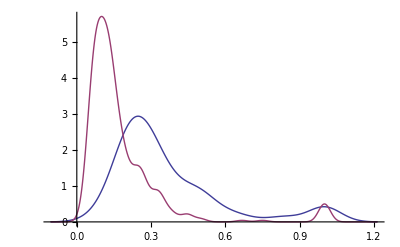

```mathematica
SmoothHistogram@{hif[[2;;,35]],frf[[2;;,35]]}
```

Consensus - ranksum is not a great measure of features. Its hard to understand how to map p-values onto the “goodness” of a feature.

```mathematica
CMI[features_,featurelabels_]:=Module[{p0,p1,xdist,x0dist,x1dist,dlog},
xdist=SmoothKernelDistribution[features];
x0dist=SmoothKernelDistribution[
Select[Transpose@{features,featurelabels},#[[2]]==0&][[;;,1]]
];
x1dist=SmoothKernelDistribution[
Select[Transpose@{features,featurelabels},#[[2]]==1&][[;;,1]]
];
p0 = Count[featurelabels,0]/Length@featurelabels;p1=Count[featurelabels,1]/Length@featurelabels;
dlog =Piecewise[{{0,#≤0},{Log[#],True}}]&;
Return[
p0 NIntegrate[PDF[xdist,x]PDF[x0dist,x]dlog[PDF[x0dist,x]/PDF[xdist,x]/p0],{x,-2,10}]+p1 NIntegrate[PDF[xdist,x]PDF[x1dist,x]dlog[PDF[x1dist,x]/PDF[xdist,x]/p1],{x,-2,10}]
]
]
```

```mathematica
HMI[p1_,p2_]:=With[{l=Length@p1+Length@p2},Entropy[p1~Join~p2]-(Length@p1/l Entropy[p1] + Length@p2/l Entropy[p2])]
```

```mathematica
SortBy[#,-#[[-1]]&]&@Transpose[{Range[Length@hif[[1]]],hif[[1]],N@HMI[hif[[2;;,#]],frf[[2;;,#]]]&/@Range[Length@hif[[1]]]}]//TableForm
```

43 | markov_N | 0.363223
44 | markov_R | 0.363223
35 | compressed_mean_leaf_height__compress_of_length | 0.345139
36 | compressed_mean_leaf_height__compress_of_depth | 0.344511
47 | markov_NN | 0.341404
49 | compressed_markov_N | 0.330902
50 | compressed_markov_R | 0.330902
46 | markov_RN | 0.319747
14 | mean_leaf_height__length | 0.308294
15 | mean_leaf_height__depth | 0.305894
4 | num_normal__num_nodes | 0.299564
5 | num_reverse__num_nodes | 0.295401
45 | markov_NR | 0.277838
16 | stdev_leaf_height__length | 0.266537
33 | compressed_mean_range_reverse__compress_of_length | 0.264866
21 | stdev_inorder_pos_reverse__num_nodes | 0.261726
42 | compressed_stdev_inorder_pos_reverse__compress_of_num_nodes | 0.261726
12 | mean_range_reverse__length | 0.258315
52 | compressed_markov_RN | 0.251976
10 | max_range_reverse__length | 0.251925
31 | compressed_max_range_reverse__compress_of_length | 0.251925
26 | compressed_num_reverse__compress_of_num_nodes | 0.251665
20 | mean_inorder_pos_reverse__num_nodes | 0.24575
41 | compressed_mean_inorder_pos_reverse__compress_of_num_nodes | 0.24575
24 | compressed_num_nodes__compress_of_length | 0.241817
48 | markov_RR | 0.237346
13 | stdev_range_reverse__length | 0.237071
9 | reverse_max_depth__depth | 0.230479
8 | reverse_max_depth__length | 0.229804
28 | compressed_depth__compress_of_length | 0.227689
30 | compressed_reverse_max_depth__compress_of_depth | 0.223953
25 | compressed_num_normal__compress_of_num_nodes | 0.216782
29 | compressed_reverse_max_depth__compress_of_length | 0.215284
34 | compressed_stdev_range_reverse__compress_of_length | 0.21152
51 | compressed_markov_NR | 0.209821
53 | compressed_markov_NN | 0.195847
17 | stdev_leaf_height__depth | 0.187172
54 | compressed_markov_RR | 0.163071
7 | depth__length | 0.161291
32 | compressed_min_range_reverse__compress_of_length | 0.148391
11 | min_range_reverse__length | 0.12749
40 | compressed_min_leaf_height__compress_of_depth | 0.119514
19 | min_leaf_height__depth | 0.118912
6 | depth__<lambda> | 0.10791
38 | compressed_stdev_leaf_height__compress_of_depth | 0.104665
37 | compressed_stdev_leaf_height__compress_of_length | 0.0997496
18 | min_leaf_height__length | 0.0849068
39 | compressed_min_leaf_height__compress_of_length | 0.0848772
23 | compressed_num_nodes__<lambda> | 0.0838806
1 | length__<lambda> | 0.0707184
22 | compressed_length__<lambda> | 0.0707184
27 | compressed_depth__<lambda> | 0.0683356
2 | num_nodes__<lambda> | 0.0674601
3 | num_nodes__length | 0.0245782

```mathematica
Discretize[val_] := If[Chop[val] == 0, 0, Ceiling[val] ]
FrequencyPad[one_, two_]:= Module[{hash1, hash2, intersect},
hash1=Hash[#1[[1]]]->#1&/@one;
hash2=Hash[#1[[1]]]->#1&/@two;
intersect= hash1[[;;,1]]~Intersection~hash2[[;;,1]];
Return[{intersect/.hash1, intersect/.hash2}];
];
MutualInformation[features_, featurelabels_, col_]:=Module[{yprob,xprob,xyprob1, xyprob0,i},
(*yprob = p(y), xprob = p(x), xyprob1 = p(x|y=1), xyprob0= p(x|y=0) *)
yprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[featurelabels[[;;]] ] ];
xprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[Discretize/@features[[;;, col]] ] ];
xyprob1 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==1&][[;;,2]]]
];
xyprob0 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==0&][[;;,2]]]
];
Return[  yprob[[2,2]] * (xyprob1[[;;,2]].Log@xyprob1[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob1, xprob] ]) +
yprob[[1,2]] * (xyprob0[[;;,2]].Log@xyprob0[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob0, xprob] ])];
];
```

```mathematica
SortBy[#,-#[[2]]&]&@Table[{#3[[c]],N@MutualInformation[Transpose@{Rescale[#1[[;;,c]]~Join~#2[[;;,c]] ]},ConstantArray[1,Length@#1]~Join~ConstantArray[0,Length@#2],1]},{c,1,Length@#1[[1]]}]&[hif[[2;;]],frf[[2;;]],hif[[1]]]//TableForm
```

markov_RR | 0.124757
compressed_markov_RR | 0.101942
stdev_range_reverse__length | 0.0415849
compressed_stdev_inorder_pos_reverse__compress_of_num_nodes | 0.0347561
stdev_inorder_pos_reverse__num_nodes | 0.0347561
compressed_stdev_range_reverse__compress_of_length | 0.0277011
compressed_markov_RN | 0.020526
markov_RN | 0.020526
markov_NN | 0.0189895
compressed_stdev_leaf_height__compress_of_depth | 0.0185304
compressed_stdev_leaf_height__compress_of_length | 0.0185304
stdev_leaf_height__depth | 0.0171632
stdev_leaf_height__length | 0.0171632
compressed_markov_R | 0.0109877
compressed_max_range_reverse__compress_of_length | 0.0109877
compressed_mean_inorder_pos_reverse__compress_of_num_nodes | 0.0109877
compressed_mean_range_reverse__compress_of_length | 0.0109877
compressed_min_range_reverse__compress_of_length | 0.0109877
compressed_num_reverse__compress_of_num_nodes | 0.0109877
compressed_reverse_max_depth__compress_of_depth | 0.0109877
compressed_reverse_max_depth__compress_of_length | 0.0109877
markov_R | 0.0109877
max_range_reverse__length | 0.0109877
mean_inorder_pos_reverse__num_nodes | 0.0109877
mean_range_reverse__length | 0.0109877
min_range_reverse__length | 0.0109877
num_reverse__num_nodes | 0.0109877
reverse_max_depth__depth | 0.0109877
reverse_max_depth__length | 0.0109877
compressed_markov_N | 0.00711246
compressed_min_leaf_height__compress_of_length | 0.00711246
compressed_num_normal__compress_of_num_nodes | 0.00711246
markov_N | 0.00711246
min_leaf_height__length | 0.00711246
num_nodes__length | 0.00711246
num_normal__num_nodes | 0.00711246
compressed_markov_NN | 0.00552731
compressed_depth__<lambda> | 0.00546457
compressed_num_nodes__<lambda> | 0.00546457
depth__length | 0.0035464
mean_leaf_height__length | 0.0035464
compressed_length__<lambda> | 0.00265976
depth__<lambda> | 0.00265976
length__<lambda> | 0.00265976
num_nodes__<lambda> | 0.00265976
compressed_markov_NR | 0.00123055
markov_NR | 0.00123055
compressed_depth__compress_of_length | 0.000810052
compressed_mean_leaf_height__compress_of_depth | 0.000810052
compressed_mean_leaf_height__compress_of_length | 0.000810052
compressed_min_leaf_height__compress_of_depth | 0.000810052
compressed_num_nodes__compress_of_length | 0.000810052
min_leaf_height__depth | 0.000810052
mean_leaf_height__depth | 0.000404565

# Logistic Regression

```mathematica
H[X_,θ_,hθ_] := Table[Sum[-X[[i,j]]X[[i,k]]hθ[X[[i]], θ](1-hθ[X[[i]], θ]),{i,1,Length[X]}], {j,1,Length[θ]},{k,1,Length[θ]}]
Delθ[X_,Y_,θ_,hθ_]:=Table[Sum[(Y[[i]]-hθ[X[[i]],θ])X[[i,j]],{i,1,Length[X]}],{j,1,Length[θ]}]
Newton[θ_,X_,Y_,hθ_]:= θ- Inverse[H[X,θ,hθ]].Delθ[X,Y,θ,hθ]
Newton[θ_,{X_,Y_,hθ_}]:= Newton[θ,X,Y,hθ]
```

```mathematica
Iterate[func_,n_,initial_,consts_]:=Module[{temp,i},
temp=initial;
For[i=0,i<n,i++,
 temp =func[temp,consts];
];
Return[temp];
];
```

```mathematica
XX=Table[Join[{1.},#[[i]]],{i,1,Length@#}]&@(hifeatures~Join~frfeatures);YY=ConstantArray[{1.}, Length@hifeatures]~Join~ConstantArray[{0.},Length@frfeatures];
```

```mathematica
Clear[sol]
sol[X_,Y_,θ_]:=Iterate[Newton, 100, θ, {X,Y,1/(1+ⅇ^(-#1.Flatten[#2]))&}]
```

```mathematica
sol[XX,YY,{0.,0.,0.}]
```

```mathematica
Show[
BubbleChart[{Flatten/@Tally@hifeatures,Flatten/@Tally@frfeatures}],
Plot[Solve[0.2542553502946426+-0.34731543843304x1+0.33441826042367423x2==0,x2][[1,1,2]],{x1,0,40},PlotStyle->Thick]
]
```

-Graphics-

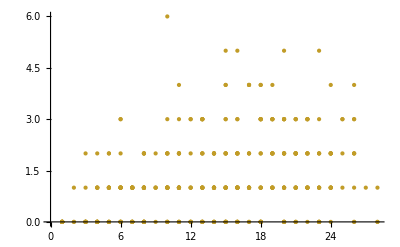

```mathematica
ListPlot@frf[[2;;,{4,5}]]
```

```mathematica
Norm[{1,1},10]
2^(1/10)
```

2^(1/10)

2^(1/10)

# Density Based Estimation

```mathematica
Clear@denseclassifier
denseclassifier[p_:10,k_:1,w_:0.2]:=With[{mins=Min/@Transpose@#[[;;,1]],maxs=Max/@Transpose@#[[;;,1]]},Show[
ContourPlot[Norm[#[[2]] Exp[-k Norm[{x,y}-#[[1]] ]]&/@#,p]/Length[#]^(1/p),{x,mins[[1]]-(maxs-mins)[[1]]*w,maxs[[1]]+(maxs-mins)[[1]]*w},{y,mins[[2]]-(maxs-mins)[[2]]*w,maxs[[2]]+(maxs-mins)[[2]]*w},PlotLegends->Automatic,PlotRange->All, Contours->Table[0.05i,{i,0,20}]]
]]&;
```

```mathematica
Manipulate[denseclassifier[E^p,k][{ {{1,1}, 1},{{3,4},1}}],{p,0,6},{k,0.1,5}]
```

```mathematica
denseclassifier[10,0.5][hif[[2;;,{1,17}]]]
denseclassifier[10,0.5][frf[[2;;,{1,17}]]]
```

-Graphics-

-Graphics-

# Topological Data Analysis

```mathematica
Needs["HierarchicalClustering`"]
```

### Functions

```mathematica
clusterorder::usage="clusterorder[dmat] rearranges the distancematrix to be in the order of a dendrogram created by the Agglomerate function. This is good to try an ";
clusterorder[dmat_]:=dmat[[ #,#]]&@ClusterFlatten@DirectAgglomerate[#,Linkage->"Ward"]&@dmat
```

```mathematica
dmat = DistanceMatrix@hif[[2;;]];
```

```mathematica
ArrayPlot[clusterorder@dmat,ColorFunction->Function[{z},GrayLevel[z^0.5]]]
```

DirectAgglomerate::ties: 5 ties have been detected; reordering input may produce a different result.

-Graphics-

```mathematica
Manipulate[Plot[Evaluate[(Juxt@@makebinfunc[n,o])@x],{x,0,1},PlotStyle->{Green,Red}],{n,Table[i,{i,5,15}]},{o, 0,0.5}]
```

```mathematica
Clear@Juxt
Juxt[fs__]:=With[{x=#},#@x&/@{fs}]&
```

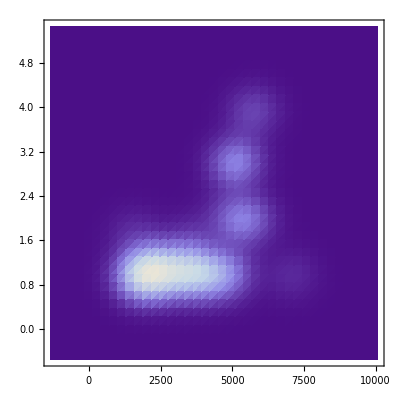

```mathematica
(* This is Cmax (max centrality). You can also use Mean, Geometric Mean, Harmonic Mean, etc *)
centrality[n_,distances_]:=Norm[distances,n] 
density[n_,k_,distances_]:=Norm[Exp[-k #]&/@distances,n]
SmoothDensityHistogram[Juxt[centrality[10,#]&,density[1,1,#]&]/@dmat,PlotRange->All]
```

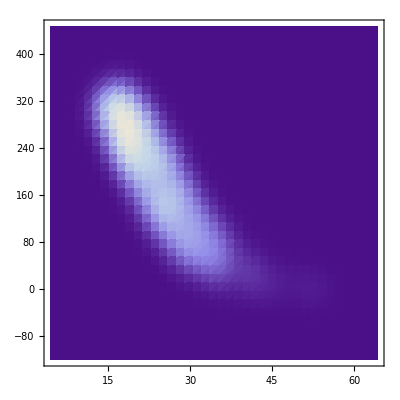
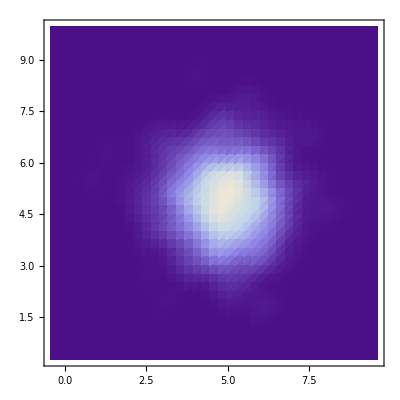

```mathematica
{
SmoothDensityHistogram[Juxt[centrality[Infinity,#]&,density[1,1,#]&]/@DistanceMatrix@#,PlotRange->All],
SmoothDensityHistogram[#,PlotRange->All]
}&@RandomVariate[NormalDistribution[5,1],{1000,2}]
```

```mathematica
GeneralClusterSplit[n_,cluster_]:=If[Head@cluster===Cluster,ClusterSplit[cluster,n],{cluster}];
GeneralClusterFlatten[c_]:=If[Head@c===Cluster, ClusterFlatten@c,If[Head@c===List,c,{ c}]];Clear@makebinfunc
makebinfunc[nbins_,overlap_]:=Juxt@@{Floor[nbins #]+1&, If[overlap /nbins - (nbins #-Floor[nbins #])/nbins >0,Floor[nbins #],Null]&}
```

```mathematica
Clear@AssignBins
AssignBins::usage="OverlappingBin[rows, metric, nbins, overlap] 
	rows: 2D list such that metric[[i]] is for row[[i]] 
	metric: some metric by which to bin the rows (eg, centrality) 
	nbins: number of bins to bin into
	overlap: fractional overlap of the bins, in both directions. range (0,1)
";
AssignBins[metric_, binfunc_]:= Select[Flatten[MapIndexed[With[{index=#2[[1]]},{index,#}&/@binfunc@#]&,metric],1],Not@SameQ[#[[-1]],Null]&]
CategoriesAndOverlaps [assignments_]:=Juxt[
{#[[1,2]],#[[;;,1]]}&/@GatherBy[#, #[[2]]&]&,
Juxt[#[[1,1]]&,#[[;;,2]]&]/@Select[GatherBy[#,First],Length@#>1&]&
]@assignments;
ClusteredBins[dfunc_,bins_,linkage_:"Ward"]:= MapAt[If[Head@#===Cluster,#,{#}]&@Agglomerate[#,DistanceFunction->(dfunc),Linkage->linkage ]&,#,2]&/@bins;
```

```mathematica
{bins,overlaps} =CategoriesAndOverlaps@AssignBins[Rescale[centrality[100,#]&/@dmat],makebinfunc[4, 0.75]];
(Length/@bins[[;;,2]])/Length@dmat//N
Length@overlaps/Length@dmat//N
groups=Quiet@ClusteredBins[(dmat[[ #1,#2 ]]&),bins];
clusters=(MapAt[GeneralClusterFlatten/@GeneralClusterSplit[3,#]&,#,2]&/@groups);
lookup=Dispatch[#[[1]]->#[[2]]&/@clusters];
idcluster=#[[1]]->#[[2]]&/@enumerate[Flatten[#,1]&@clusters[[;;,2]]];
clusterid = Dispatch[Reverse/@idcluster];
links=(With[{x=#},First@Select[#,MemberQ[#,First@x]&]/.clusterid&/@(x[[2]]/.lookup)]&/@overlaps);
Graph[idcluster[[;;,1]],#[[1]]<->#[[2]]&/@(DeleteDuplicates@links),VertexLabels->"Name",VertexSize->(MapAt[5 Length@#/Length@dmat&,#,2]&/@idcluster)]
```

{0.45977,0.264368,0.344828,0.402299,0.287356,0.0114943}

0.770115

-Graphics-

```mathematica
SmoothHistogram[#,PlotStyle->{Red}]&/@Transpose [
hif[[ 1 + Flatten[{11,8}/.idcluster] ]]
]
```